```mathematica
signalBinaryCode = ReadList["C:\\Users\\22153\\Documents\\leti\\foit\\IDZ4\\signal\\signaldigit18.txt", {Number, Number, Number, Number, Number, Number, Number, Number}];
signalAnalog = Table[FromDigits[signalBinaryCode[[i]], 2], {i, 1, Length@signalBinaryCode}];
ListPlay[signalAnalog, SampleRate->44100]
```

-Graphics-

График сигнала

```mathematica
t = 3.75;
dt = t / Length@signalBinaryCode;
signalPlot = Table[{(i - 1) * dt, signalAnalog[[i]]}, {i, 1, Length@signalBinaryCode}];
ListPlot[signalPlot,Filling->Axis,PlotRange->Full,PlotStyle-> Orange]
```

-Graphics-

Спектр сигнала

```mathematica
signalFourier = Fourier[signalAnalog];
df = 1 / t;
outN = Length@signalFourier;
signalFourierAbs  = Table[{2π df (i-1), Abs@signalFourier[[i]]},{i,2,outN}];
ListPlot[signalFourierAbs,Filling->Axis,PlotRange->Full,PlotStyle-> Orange]
```

-Graphics-

Использование фильтра Баттерворта

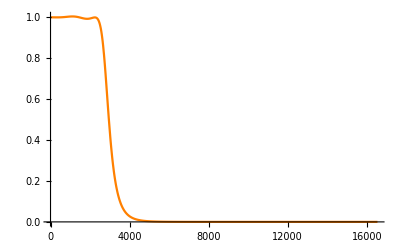

```mathematica
coef = 2.25;
R = 50;
C1 = 5.9 * 10^-6 * coef;
C2 = 5.4 * 10^-6 * coef;
C3 = 4.1 * 10^-6 * coef;
C4 = 2.4 * 10^-6 * coef;
C5 = 497.9 * 10^-9 * coef;
L1 = 12.4 * 10^-3 * coef;
L2 = 14.4 * 10^-3 * coef;
L3 = 12 * 10^-3 * coef;
L4 = 8.3 * 10^-3 * coef;
L5 = 3.7 * 10^-3 * coef;
Zpar5[ω_] = 1/(I ω C5+1/R);
Zpar4[ω_] = 1/(I ω C4+1/(I ω L5 + Zpar5[ω]));
Zpar3[ω_] = 1/(I ω C3+1/(I ω L4 + Zpar4[ω]));
Zpar2[ω_] = 1/(I ω C2+1/(I ω L3 + Zpar3[ω]));
Zpar[ω_] = 1/(I ω C1+1/(I ω L2 + Zpar2[ω])); 
I1[ω_] = Uin/(I ω L1 + Zpar[ω]);

Upar1[ω_] = I1[ω]*Zpar[ω];
I2[ω_] = Upar1[ω]/(I ω L2 + Zpar2[ω]);

Upar2[ω_] = I2[ω] * Zpar2[ω];
I3[ω_] = Upar2[ω]/(I ω L3+ Zpar3[ω]);

Upar3[ω_] = I3[ω] * Zpar3[ω];
I4[ω_] = Upar3[ω]/(I ω L4+ Zpar4[ω]);

Upar4[ω_] = I4[ω] * Zpar4[ω];
I5[ω_] = Upar4[ω]/(I ω L5+ Zpar5[ω]);

Upar5[ω_] = I5[ω] * Zpar5[ω];
Uout[ω_] = Upar5[ω];

H[ω_]= Uout[ω]/Uin;

Hlist=Table[Abs@H[i],{i,1,outN}];
signalFourierFiltered = signalFourier*Hlist;

Plot[Abs@H[ω],{ω, 1, outN/10}, PlotRange->Full, PlotStyle-> Orange]
```

Спектр сигнала после фильтрации

```mathematica
signalFourierFilteredTable = Table[{2π df (i-1), Abs@signalFourierFiltered[[i]]},{i,2,outN}];
ListPlot[signalFourierFilteredTable , Filling->Axis,PlotRange->Full, PlotStyle-> Orange]
```

-Graphics-

График сигнала после фильтрации

```mathematica
signalFiltered  = InverseFourier[signalFourierFiltered];
signalFilteredTable =  Table[{( i-1)*dt,Re@signalFiltered[[i]]},{i,1,Length@signalBinaryCode}];
ListPlot[signalFilteredTable,Filling->Axis,PlotRange->Full, PlotStyle->Orange]
```

-Graphics-

Воспроизведение звука после сигнала

```mathematica
ListPlay[Re@signalFiltered , SampleRate->44100]
```

-Graphics-